## Metricas del fluido perfecto e indice del politropo

```mathematica
ξ[r_]:=Log[(A-(B)*(r^2))^2];
μ[r_]:=-Log[1+(c)(r^2)((A)-3(r^2)(B))^(-2/3)];
Γ:=1+1/n
```

## Ecuación diferencial master para la obtención de la deformación del espacio f

```mathematica
DSolve[f'[r]/r+f[r]/r^2==-(Ka)^(Γ)(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)),f[r],r]
```

{{f[r]→(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))+C[1]/r}}

```mathematica
f[r_]:=(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))
```

## Ecuación diferencial para la obtención de la derivada de la deformación del tiempo

```mathematica
gprime[r_]:=(r/(Exp[-μ[r]]+f[r]))(κ Ka((Ka)^(Γ)/κ(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)))^(Γ) -f[r](1/r^2+ξ'[r]/r))
```

```mathematica
gprime[r]//FullSimplify
```

(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
gprime[r_]:=(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

## Cambio en la geometria del espacio-tiempo

### Derivada de ν, para el tiempo

```mathematica
νprime[r_]:=D[ξ[r],r]+gprime[r]
νprime[r]//FullSimplify
```

-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
νprime[r_]:=-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

### Cambio de λ, para el espacio

```mathematica
λ[r_]:=-Log[Exp[-μ[r]]+f[r]]
```

```mathematica
λ[r]//FullSimplify
```

-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))]

```mathematica
λ[r_]:=-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))];
```

## Ecuaciones de Einstein

### Densidad Efectiva

```mathematica
ρ[r_]:=1/(κ r^2)(1-ⅇ^(-λ[r])(1-r D[λ[r],r]));
ρ[r]//FullSimplify
```

-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ)

```mathematica
ρ[r_]:=-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ);
```

### Presión efectiva

```mathematica
Pr[r_]:=-1/(κ r^2)(1-ⅇ^(-λ[r])(1+r *νprime[r]));
Pr[r]//FullSimplify
```

(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)/((A-3 B r^2) (A-B r^2) κ)

```mathematica
Pr[r_]:=(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)/((A-3 B r^2) (A-B r^2) κ)
```

### Presión Tangencial efectiva

```mathematica
Pt[r_]:=Exp[-λ[r]]/(4κ)(2νprime'[r]+(νprime[r])^2-λ'[r]νprime[r]+(2(νprime[r]-λ'[r]))/r);
Pt[r]//Simplify
```

((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)

```mathematica
Pt[r_]:=((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)
```

## Resolución de la integral numérica de gprima, mediante MATLAB

```mathematica
gnume:=-14.431039405906983
```

```mathematica
νnumer[r_]:=ξ[r]+gnume
```

## Aplicación de las condiciones de frontera

```mathematica
Solve[Exp[-λ[R]]==1-(2M)/R,c]
```

{{c→-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)}}

```mathematica
c:=-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)
```

```mathematica
NSolve[Exp[νnumer[R]]==1-(2M)/R,A]
```

{{A→0.0000501354 (19946. B R^2-(2.71341×10^7 √(-2. M+R))/(√R))},{A→0.0000501354 (19946. B R^2+(2.71341×10^7 √(-2. M+R))/(√R))}}

```mathematica
A:=0.0000501353654868144 (19946. B R^2-(2.7134149017295845*^7 √(-2. M+R))/(√R))
```

### Damos las constantes que usamos en la integración

```mathematica
B=0.45;
Ka=0.55;
n=0.5;
κ=8*π;
R=1;
```

## Intercambio Energético

```mathematica
DEnergy[r_]:=gprime[r]/(2κ)×Exp[-μ[r]]/r(ξ'[r]+μ'[r])
DEnergy[r]/.{M->u R,r->x R}//FullSimplify
```

-((2.66094×10^-10 x ((0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 x^2) (((-0.9-1360.38 √(1-2. u))^(2/3) u (-0.000992369+3. √(1-2. u)+0.00165395 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033079+1. √(1-2. u)+0.000992369 x^2)))^3.+(-0.9-1360.38 √(1-2. u))^(2/3) u (-4.66777+14111. √(1-2. u)+23.3388 x^2)) (-5183.7 (-0.9-1360.38 √(1-2. u))^(2/3) u^2+(0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033079+1. √(1-2. u)+0.000992369 x^2)+(-0.9-1360.38 √(1-2. u))^(2/3) u (2591.85-1.71471 √(1-2. u)+2.11524×10^-16 √(1-2. u) x^2-0.00141803 x^4)))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2 (-0.00033079+1. √(1-2. u)+0.000992369 x^2) (1. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))))

```mathematica
DEnergy[x_]:=-((2.660938384176462*^-10 x ((0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (-0.0003307898100758094+1. √(1-2. u)+0.0003307898100758094 x^2) (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.000992369430227428+3. √(1-2. u)+0.0016539490503790465 x^2))/((0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2)))^3.+(-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-4.667769792877099+14110.984228345349 √(1-2. u)+23.338848964385495 x^2)) (-5183.697745982449 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u^2+(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2)+(-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (2591.8491565962486-1.7147143928839352 √(1-2. u)+2.1152393329287684*^-16 √(1-2. u) x^2-0.001418025120890834 x^4)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2 (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2) (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3))))
```

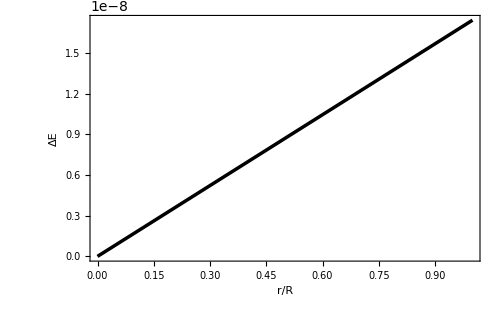

```mathematica
solu1:=Re[DEnergy[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ΔE"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
DEnergy[x]/.{x->√(x^2+y^2)}//FullSimplify
```

-((2.66094×10^-10 √(x^2+y^2) ((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2)) (((-0.9-1360.38 √(1-2. u))^(2/3) u (-0.000992369+3. √(1-2. u)+0.00165395 (x^2+y^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033079+1. √(1-2. u)+0.000992369 (x^2+y^2))))^3.+(-0.9-1360.38 √(1-2. u))^(2/3) u (-4.66777+14111. √(1-2. u)+23.3388 (x^2+y^2))) (-5183.7 (-0.9-1360.38 √(1-2. u))^(2/3) u^2+(0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033079+1. √(1-2. u)+0.000992369 (x^2+y^2))+(-0.9-1360.38 √(1-2. u))^(2/3) u (2591.85-1.71471 √(1-2. u)+2.11524×10^-16 √(1-2. u) (x^2+y^2)-0.00141803 (x^2+y^2)^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.00033079-1. √(1-2. u)-0.00033079 (x^2+y^2))^2 (-0.00033079+1. √(1-2. u)+0.000992369 (x^2+y^2)) (1. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))

```mathematica
dEnergy[x_,y_]:=-((2.660938384176462*^-10 √(x^2+y^2) ((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.0003307898100758094+1. √(1-2. u)+0.0003307898100758094 (x^2+y^2)) (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.000992369430227428+3. √(1-2. u)+0.0016539490503790465 (x^2+y^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 (x^2+y^2))))^3.+(-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-4.667769792877099+14110.984228345349 √(1-2. u)+23.338848964385495 (x^2+y^2))) (-5183.697745982449 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u^2+(0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 (x^2+y^2))+(-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (2591.8491565962486-1.7147143928839352 √(1-2. u)+2.1152393329287684*^-16 √(1-2. u) (x^2+y^2)-0.001418025120890834 (x^2+y^2)^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 (x^2+y^2))^2 (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 (x^2+y^2)) (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))
```

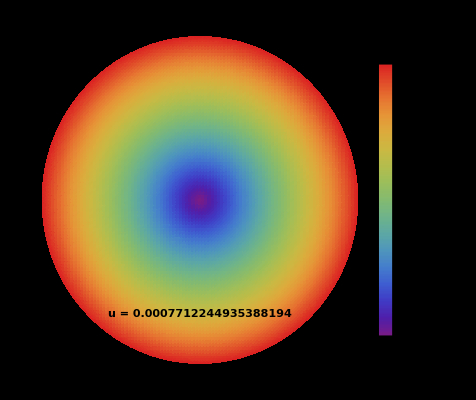

```mathematica
DensityPlot[Re[dEnergy[x,y]]/.{u->0.0007712244935388194},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.0007712244935388194",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Condiciones de aceptabilidad

### Sector material

```mathematica
Pr[r]/.{M-> u R, r->x R}//FullSimplify
```

(2.15×10^-8 (-0.81+2448.68 √(1-2. u)+2.43 x^2+37.4148 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.00033079 x^2) (-0.00033079+1. √(1-2. u)+0.000992369 x^2)+(-0.9-1360.38 √(1-2. u))^(2/3) u (0.45-1360.38 √(1-2. u)-1.35 x^2)^(1/3) (-0.771621+2332.66 √(1-2. u)+3.85811 x^2)))/((-0.00033079+1. √(1-2. u)+0.00033079 x^2) (-0.00033079+1. √(1-2. u)+0.000992369 x^2))

```mathematica
Prg[x_]:=(2.1500044470142357*^-8 (-0.81+2448.6848606804633 √(1-2. u)+2.43 x^2+37.41479218732841 (((-0.9000000000000002-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2)+(-0.9000000000000002-1360.3804781558129 √(1-2. u))^(2/3) u (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(1/3) (-0.7716214767977709+2332.6639856921024 √(1-2. u)+3.858107383988855 x^2)))/((-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2))
```

```mathematica
Solve[Prg[1]==0,u]
```

{{u→-56.0541},{u→0.000771224},{u→56.047-0.00699929 ⅈ},{u→56.047+0.00699929 ⅈ}}

```mathematica
Prg[1]/.u->0.0007712244935388194
```

0.

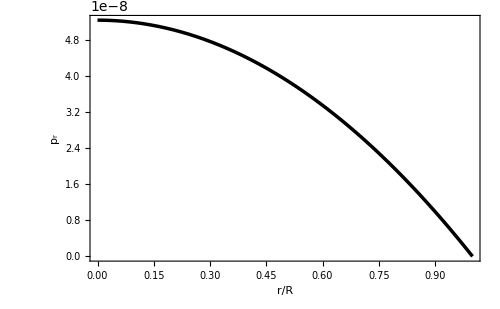

```mathematica
solu1:=Re[Prg[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Full]
```

```mathematica
Pt[r]/.{M-> u R, r->x R}//Simplify
```

(1.45221×10^-15 (1-(2. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2)/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))) (-1.19921×10^7 x^2 (0.00033079-1. √(1-2. u)-0.000992369 x^2)^2 (1. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))^2+1.81265×10^10 (0.00033079-1. √(1-2. u)-0.000992369 x^2)^2 (-0.00033079+1. √(1-2. u)+0.00033079 x^2) (1. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))^2+0.513514 (-0.9-1360.38 √(1-2. u))^(2/3) u x^2 (-2. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2+(0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3)) (-2.51757×10^9 (-0.00033079+1. √(1-2. u))^3-7.49507×10^6 (0.00033079-1. √(1-2. u))^2 x^2-6335.97 (-0.00033079+1. √(1-2. u)) x^4-1.36688 x^6+5.03514×10^9 (-0.00033079+1. √(1-2. u)) (0.00033079-1. √(1-2. u)-0.000992369 x^2)^2-2.67618×10^6 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^2. (-0.00033079+1. √(1-2. u)+0.00033079 x^2)^3)+0.5 x^2 (0.45-1360.38 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9-1360.38 √(1-2. u))^(2/3) u x^2-1.8 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3)-0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 x^2)-388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 x^2))^2-4. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2 (0.45-1360.38 √(1-2. u)-1.35 x^2) (0.45-1360.38 √(1-2. u)-0.45 x^2)^2 (0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 x^2)+388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 x^2))-1. (0.45-1360.38 √(1-2. u)-1.35 x^2)^2 (0.45-1360.38 √(1-2. u)-0.45 x^2) (-2. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2+(0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3)) (0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 x^2)+388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 x^2))+2. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2 (0.45-1360.38 √(1-2. u)-1.35 x^2) (0.45-1360.38 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9-1360.38 √(1-2. u))^(2/3) u x^2+1.8 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3)+0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 x^2)+388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 x^2))-1. (0.45-1360.38 √(1-2. u)-1.35 x^2) (0.45-1360.38 √(1-2. u)-0.45 x^2) (-2. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2+(0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3)) (7.40254×10^6 (-0.9-1360.38 √(1-2. u))^(2/3) u (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2+4897.37 (-0.00033079+1. √(1-2. u)+0.000992369 x^2) (1. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-1360.38 √(1-2. u)-1.35 x^2) (0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 x^2)+388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 x^2)))))/((0.00033079-1. √(1-2. u)-0.000992369 x^2)^2 (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2 (1. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))^2)

```mathematica
Ptg[x_]:=(1.4522072115322137*^-15 (1-(2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2)/((0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3))) (-1.19921150938514*^7 x^2 (0.00033078981007580934-1. √(1-2. u)-0.000992369430227428 x^2)^2 (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3))^2+1.8126488072747894*^10 (0.00033078981007580934-1. √(1-2. u)-0.000992369430227428 x^2)^2 (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2) (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3))^2+0.5135140928089168 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2 (-2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2+(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3)) (-2.517567787881653*^9 (-0.00033078981007580934+1. √(1-2. u))^3-7.495071933657125*^6 (0.00033078981007580934-1. √(1-2. u))^2 x^2-6335.972077010699 (-0.00033078981007580934+1. √(1-2. u)) x^4-1.366875 x^6+5.035135575763303*^9 (-0.00033078981007580934+1. √(1-2. u)) (0.00033078981007580934-1. √(1-2. u)-0.000992369430227428 x^2)^2-2.676178798525445*^6 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^2. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2)^3)+0.5 x^2 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2-1.8 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3)-0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2)-388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 x^2))^2-4. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2) (0.45-1360.3804781558129 √(1-2. u)-0.45 x^2)^2 (0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2)+388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 x^2))-1. (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^2 (0.45-1360.3804781558129 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2+(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3)) (0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2)+388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 x^2))+2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2) (0.45-1360.3804781558129 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2+1.8 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3)+0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2)+388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 x^2))-1. (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2) (0.45-1360.3804781558129 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2+(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3)) (7.402540181389752*^6 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2+4897.369721360927 (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2) (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2) (0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2)+388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 x^2)))))/((0.00033078981007580934-1. √(1-2. u)-0.000992369430227428 x^2)^2 (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2 (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3))^2)
```

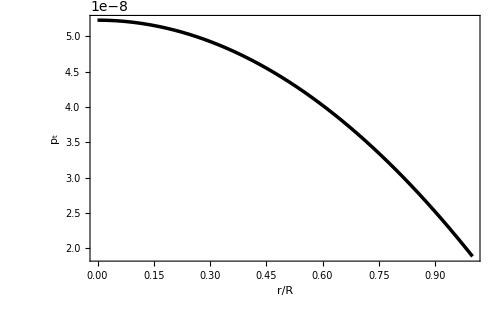

```mathematica
solu1:=Re[Ptg[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
ρ[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.0795775 (-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3))

```mathematica
ρg[x_]:=(0.07957747154594767 (-0.9000000000000002-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3)
```

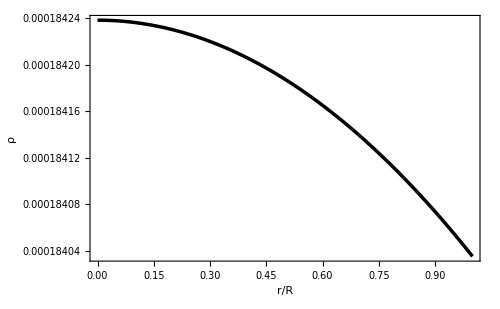

```mathematica
solu1:=Re[ρg[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Gráficas de componentes métricas del espacio-tiempo

```mathematica
Exp[νnumer[r]]/.{M->u R,r->x R}//FullSimplify
```

1. (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2

```mathematica
metric1[x_]:=0.9999999999999998 (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2
```

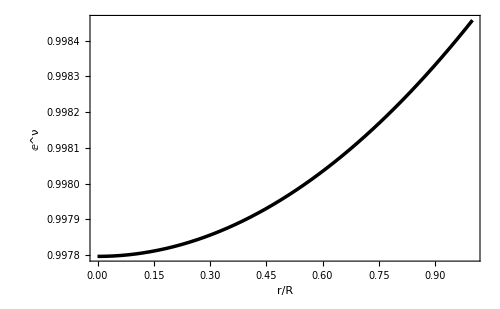

```mathematica
solu1:=Re[metric1[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^ν"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Exp[-λ[r]]/.{M-> u R, r->x R}//FullSimplify
```

1-(2. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2)/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))

```mathematica
metric2[x_]:=1-(2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2)/((0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3))
```

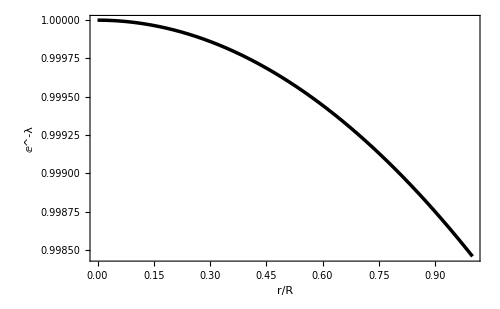

```mathematica
solu1:=Re[metric2[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^-λ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condiciones de energía

#### Condición de energía dominante

```mathematica
dec1[x_]:=ρg[x]-Prg[x];
```

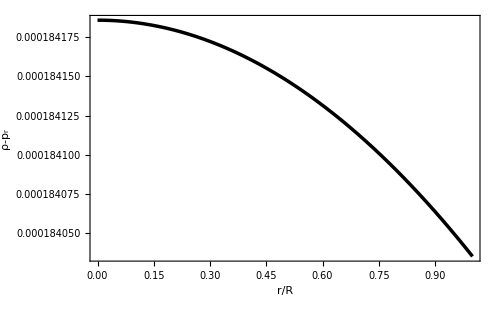

```mathematica
solu1:=Re[dec1[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
dec2[x_]:=ρg[x]-Ptg[x];
```

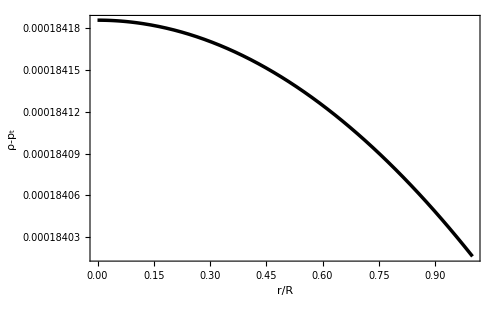

```mathematica
solu1:=Re[dec2[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Condicion de energía fuerte

```mathematica
sec[x_]:=ρg[x]-Prg[x]-2*Ptg[x];
```

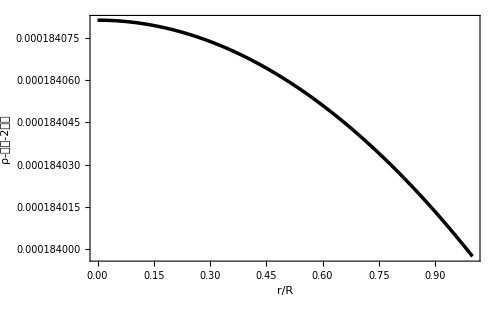

```mathematica
solu1:=Re[sec[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-𝓅𝓇-2𝓅𝓉"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Corrimiento al rojo

```mathematica
Z[r_]:=1/(√(ⅇ^(νnumer[r])))-1
```

```mathematica
Z[r]/.{M-> u R, r->x R}//FullSimplify
```

-1+1./(√((0.00033079-1. √(1-2. u)-0.00033079 x^2)^2))

```mathematica
Z[x_]:=-1+1.0000000000000002/(√((0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2))
```

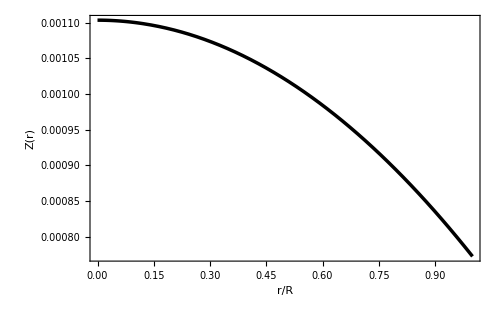

```mathematica
solu1:=Re[Z[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Z(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condición de causalidad:?

#### Velocidad Radial?

```mathematica
vr[r_]:=D[Pr[r],r]/D[ρ[r],r]
```

```mathematica
vr[r]/.{M-> u R, r->x R}//FullSimplify
```

(3.64979×10^-14 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-1360.38 √(1-2. u)-1.35 x^2) (0.45-1360.38 √(1-2. u)-0.45 x^2) (4.86+((-0.9-1360.38 √(1-2. u))^(2/3) u (0.694459-2099.4 √(1-2. u)-3.4723 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))+7.71621 (-0.9-1360.38 √(1-2. u))^(2/3) u (0.45-1360.38 √(1-2. u)-1.35 x^2)^(1/3)+0.0742586 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.00033079 x^2)-(0.247529 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2)/(-0.00033079+1. √(1-2. u)+0.000551316 x^2)+0.0247529 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.000992369 x^2))+0.286479 (0.45-1360.38 √(1-2. u)-1.35 x^2) (-0.81+2448.68 √(1-2. u)+2.43 x^2+37.4148 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.00033079 x^2) (-0.00033079+1. √(1-2. u)+0.000992369 x^2)+(-0.9-1360.38 √(1-2. u))^(2/3) u (0.45-1360.38 √(1-2. u)-1.35 x^2)^(1/3) (-0.771621+2332.66 √(1-2. u)+3.85811 x^2))+0.859437 (0.45-1360.38 √(1-2. u)-0.45 x^2) (-0.81+2448.68 √(1-2. u)+2.43 x^2+37.4148 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.00033079 x^2) (-0.00033079+1. √(1-2. u)+0.000992369 x^2)+(-0.9-1360.38 √(1-2. u))^(2/3) u (0.45-1360.38 √(1-2. u)-1.35 x^2)^(1/3) (-0.771621+2332.66 √(1-2. u)+3.85811 x^2))))/((-0.9-1360.38 √(1-2. u))^(2/3) u (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2 (1.7415×10^-7-0.000526468 √(1-2. u)-1.7415×10^-7 x^2))

```mathematica
vr[x_]:= (3.649794805791777*^-14 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2) (0.45-1360.3804781558129 √(1-2. u)-0.45 x^2) (4.86+((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.6944593291179939-2099.397587122892 √(1-2. u)-3.4722966455899695 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3)+7.71621476797771 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(1/3)+0.07425859201003344 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2)-(0.24752864003344488 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2)/(-0.00033078981007580934+1. √(1-2. u)+0.0005513163501263489 x^2)+0.02475286400334448 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2))+0.2864788975654116 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2) (-0.81+2448.6848606804633 √(1-2. u)+2.43 x^2+37.41479218732841 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2)+(-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(1/3) (-0.7716214767977709+2332.6639856921024 √(1-2. u)+3.858107383988855 x^2))+0.8594366926962349 (0.45-1360.3804781558129 √(1-2. u)-0.45 x^2) (-0.81+2448.6848606804633 √(1-2. u)+2.43 x^2+37.41479218732841 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2)+(-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(1/3) (-0.7716214767977709+2332.6639856921024 √(1-2. u)+3.858107383988855 x^2))))/((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2 (1.7415036020815318*^-7-0.0005264683339799432 √(1-2. u)-1.7415036020815318*^-7 x^2))
```

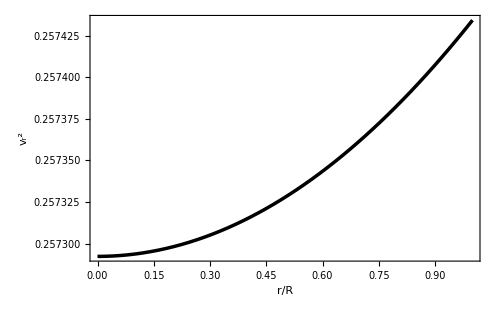

```mathematica
solu1:=vr[x]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Velocidad Tangencial

```mathematica
vt[r_]:=D[Pt[r],r]/D[ρ[r],r]
vt[r]/.{M-> u R, r->x R}
```

(-((0.0397887 2 (2. 5 (-0.285286 (-1.35+0.0000501354 (8975.7-2.71341×10^7 √(1-2. u)))^(2/3) u (0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-2.25 x^2)-0.0000202173 (1)^3. 1 (0.0000501354 (8975.7-2.71341×10^7 √(1-1))-0.45 x^2)+1.8 (-2. (-1.35+0.0000501354 (8975.7-2.71341×10^7 √(1-1)))^(2/3) u x^2+(0.0000501354 (8975.7-1)-1.35 x^2)^(2/3)))+5))/(x (0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-1.35 x^2)^2 (0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-0.45 x^2)^2 (-2. (-1.35+0.0000501354 (8975.7-2.71341×10^7 1))^(2/3) u x^2+(0.0000501354 (8975.7-1)-1.35 1)^(2/3))^3))+1/(x 1^2 1 (1)^2)+1+1-1/1+(0.0198944 (1-(2. 1 u x^2)/(1)^(2/3)) (1))/(x (1-1)^2 (1)^2 (-2. 1 u x^2+1)^2))/((0.358099 (-1.35+0.0000501354 (8975.7-2.71341×10^7 √(1-2. u)))^(2/3) u x (0.000150406 (8975.7-2.71341×10^7 √(1-2. u))-2.25 x^2))/((0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-1.35 x^2)^(8/3))-(0.358099 (-1.35+0.0000501354 (8975.7-2.71341×10^7 √(1-2. u)))^(2/3) u x)/((0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-1.35 x^2)^(5/3)))
 |  |  |  |

```mathematica
vt[x_]:={{(-((0.039788735772973836 2 (2. 5 (-0.2852856071160648 (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u)))^(2/3) u (0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-2.25 x^2)-0.00002021727205555224 (1)^3. 1 (0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-1))-0.45 x^2)+1.8 (-2. (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-1)))^(2/3) u x^2+(0.0000501353654868144 (8975.7-1)-1.35 x^2)^(2/3)))+5))/(x (0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-1.35 x^2)^2 (0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-0.45 x^2)^2 (-2. (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 1))^(2/3) u x^2+(0.0000501353654868144 (8975.7-1)-1.35 1)^(2/3))^3))+1/(x 1^2 1 (1)^2)+1+1-1/1+(0.019894367886486918 (1-(2. 1 u x^2)/(1)^(2/3)) (1))/(x (1-1)^2 (1)^2 (-2. 1 u x^2+1)^2))/((0.3580986219567646 (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u)))^(2/3) u x (0.00015040609646044319 (8975.7-2.7134149017295845*^7 √(1-2. u))-2.25 x^2))/(0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-1.35 x^2)^(8/3)-(0.3580986219567645 (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u)))^(2/3) u x)/((0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-1.35 x^2)^(5/3)))}, {{{, , , , }}}}
```

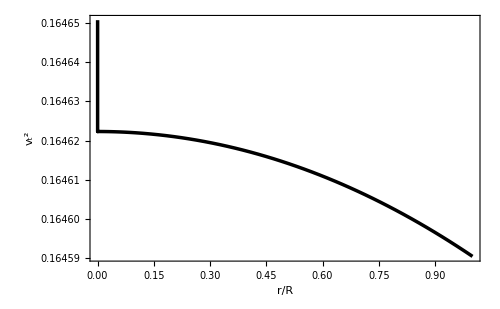

```mathematica
solu1:=Re[vt[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

## Anisotropía

```mathematica
Π[x_]:=Ptg[x]-Prg[x]
```

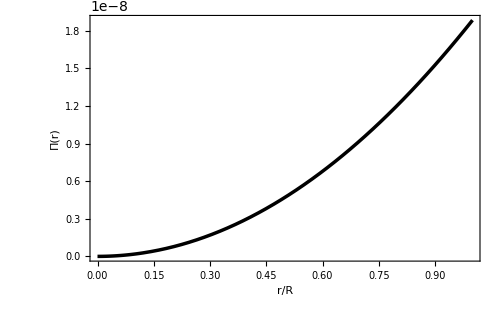

```mathematica
solu1:=Re[Π[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Π(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Π[x]/.{x->√(x^2+y^2)}//Simplify
```

-((2.15×10^-8 (-0.81+2448.68 √(1-2. u)+2.43 (x^2+y^2)+37.4148 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2)) (-0.00033079+1. √(1-2. u)+0.000992369 (x^2+y^2))+(-0.9-1360.38 √(1-2. u))^(2/3) u (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.771621+2332.66 √(1-2. u)+3.85811 (x^2+y^2))))/((-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2)) (-0.00033079+1. √(1-2. u)+0.000992369 (x^2+y^2))))+(1.45221×10^-15 (1-(2. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-1.19921×10^7 (x^2+y^2) (0.00033079-1. √(1-2. u)-0.000992369 (x^2+y^2))^2 (1. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+1.81265×10^10 (0.00033079-1. √(1-2. u)-0.000992369 (x^2+y^2))^2 (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2)) (1. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.513514 (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-2.51757×10^9 (-0.00033079+1. √(1-2. u))^3-7.49507×10^6 (0.00033079-1. √(1-2. u))^2 (x^2+y^2)-6335.97 (-0.00033079+1. √(1-2. u)) (x^2+y^2)^2-1.36688 (x^2+y^2)^3+5.03514×10^9 (-0.00033079+1. √(1-2. u)) (0.00033079-1. √(1-2. u)-0.000992369 (x^2+y^2))^2-2.67618×10^6 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^2. (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2))^3)+0.5 (x^2+y^2) (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2))-388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 (x^2+y^2)))^2-4. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1360.38 √(1-2. u)-0.45 (x^2+y^2))^2 (0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2))+388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 (x^2+y^2)))-1. (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-1360.38 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2))+388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 (x^2+y^2)))+2. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1360.38 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2))+388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 (x^2+y^2)))-1. (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1360.38 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (7.40254×10^6 (-0.9-1360.38 √(1-2. u))^(2/3) u (0.00033079-1. √(1-2. u)-0.00033079 (x^2+y^2))^2+4897.37 (-0.00033079+1. √(1-2. u)+0.000992369 (x^2+y^2)) (1. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2)) (0.0275032 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033079+1. √(1-2. u)+0.00033079 (x^2+y^2))+388.097 (-0.9-1360.38 √(1-2. u))^(2/3) u (-0.00033079+1. √(1-2. u)+0.00165395 (x^2+y^2))))))/((0.00033079-1. √(1-2. u)-0.000992369 (x^2+y^2))^2 (0.00033079-1. √(1-2. u)-0.00033079 (x^2+y^2))^2 (1. (-0.9-1360.38 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.38 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)

```mathematica
Π[x_,y_]:=-((2.1500044470142357*^-8 (-0.81+2448.6848606804633 √(1-2. u)+2.43 (x^2+y^2)+37.41479218732841 (((-0.9000000000000002-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2)) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 (x^2+y^2))+(-0.9000000000000002-1360.3804781558129 √(1-2. u))^(2/3) u (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.7716214767977709+2332.6639856921024 √(1-2. u)+3.858107383988855 (x^2+y^2))))/((-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2)) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 (x^2+y^2))))+(1.4522072115322137*^-15 (1-(2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-1.19921150938514*^7 (x^2+y^2) (0.00033078981007580934-1. √(1-2. u)-0.000992369430227428 (x^2+y^2))^2 (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+1.8126488072747894*^10 (0.00033078981007580934-1. √(1-2. u)-0.000992369430227428 (x^2+y^2))^2 (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2)) (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.5135140928089168 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-2.517567787881653*^9 (-0.00033078981007580934+1. √(1-2. u))^3-7.495071933657125*^6 (0.00033078981007580934-1. √(1-2. u))^2 (x^2+y^2)-6335.972077010699 (-0.00033078981007580934+1. √(1-2. u)) (x^2+y^2)^2-1.366875 (x^2+y^2)^3+5.035135575763303*^9 (-0.00033078981007580934+1. √(1-2. u)) (0.00033078981007580934-1. √(1-2. u)-0.000992369430227428 (x^2+y^2))^2-2.676178798525445*^6 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^2. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2))^3)+0.5 (x^2+y^2) (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2))-388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 (x^2+y^2)))^2-4. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1360.3804781558129 √(1-2. u)-0.45 (x^2+y^2))^2 (0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2))+388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 (x^2+y^2)))-1. (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-1360.3804781558129 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2))+388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 (x^2+y^2)))+2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1360.3804781558129 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2))+388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 (x^2+y^2)))-1. (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1360.3804781558129 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (7.402540181389752*^6 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 (x^2+y^2))^2+4897.369721360927 (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 (x^2+y^2)) (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2)) (0.02750318222593831 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 (x^2+y^2))+388.09697061952363 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (-0.00033078981007580934+1. √(1-2. u)+0.0016539490503790467 (x^2+y^2))))))/((0.00033078981007580934-1. √(1-2. u)-0.000992369430227428 (x^2+y^2))^2 (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 (x^2+y^2))^2 (1. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1360.3804781558129 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)
```

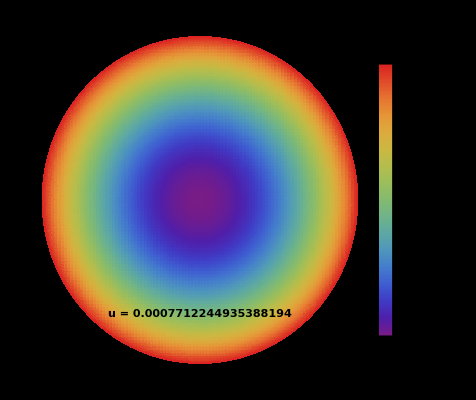

```mathematica
DensityPlot[Re[Π[x,y]]/.{u->0.0007712244935388194},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.0007712244935388194",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Cracking Gravitacional?

### Falta actualizar desede aqui para abajo, pero no cumple por lo visto en la vt^22

```mathematica
CG[x_]:=vt[x]-vr[x]
```

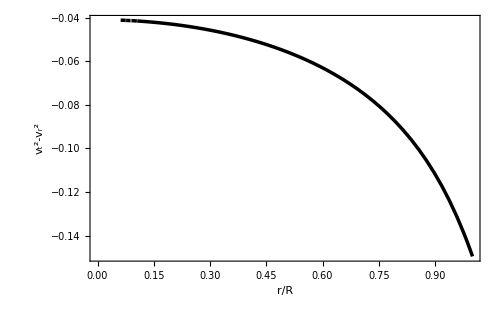

```mathematica
solu1:=CG[x]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2-v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
CG[x]/.{x->√(x^2+y^2)}
```

-((0.00472044 1 (((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2)) 1 (4.86+1/1+1+1-1/1+5.50302×10^-6 (1/1)^3. (-0.198372+1. √(1-2. u)+0.595116 (x^2+y^2))))/π+1+0.859437 (0.45-1-0.45 (1)) (-0.81+3+(-0.9-2.26846 √(1-2. u))^(2/3) u (0.45-1-1)^(1/3) (-0.829352+4.18079 √(1-2. u)+4.14676 (x^2+y^2)))))/((-0.9-2.26846 √(1-2. u))^(2/3) u (0.198372-1. √(1-2. u)-0.198372 (x^2+y^2))^2 (0.0626299-0.315719 √(1-2. u)-0.0626299 (x^2+y^2))))-(0.000917315 (0.45-2.26846 1-1.35 (x^2+y^2))^(2/3) (1)^2 (7+1))/((-0.9-2.26846 √(1-1))^(2/3) u √(x^2+y^2) (20-1-1) (1)^3 (1)^3 (1. 1 u (x^2+y^2)-0.5 1)^3)
 |  |  |  |

```mathematica
CG2d[x_,y_]:={{-((0.004720439574565849 1 (((0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2)) 1 (4.86+1/1+1+1-1/1+5.503022504604416*^-6 (1/1)^3. (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 (x^2+y^2))))/π+1+0.8594366926962349 (0.45-1-0.45 (1)) (-0.81+3+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.45-1-1)^(1/3) (-0.8293524416135881+4.180791470620436 √(1-2. u)+4.1467622080679405 (x^2+y^2)))))/((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 (x^2+y^2))^2 (0.06262985035679756-0.3157190249159851 √(1-2. u)-0.06262985035679754 (x^2+y^2))))-(0.0009173153429009489 (0.45-2.2684640056268837 1-1.35 (x^2+y^2))^(2/3) (1)^2 (7+1))/((-0.9000000000000001-2.2684640056268837 √(1-1))^(2/3) u √(x^2+y^2) (20-1-1) (1)^3 (1)^3 (1. 1 u (x^2+y^2)-0.5 1)^3)}, {{{, , , , }}}}
```

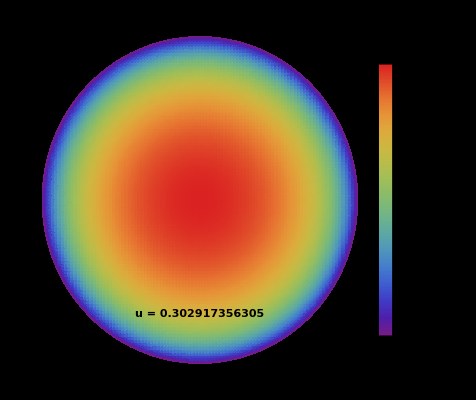

```mathematica
DensityPlot[Re[CG2d[x,y]]/.{u->0.302917356305},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.302917356305",Large,Bold],{0,-0.7}],PlotPoints->100]
```